```mathematica
<<Vilcretas`
```

VilCretas está disponible.

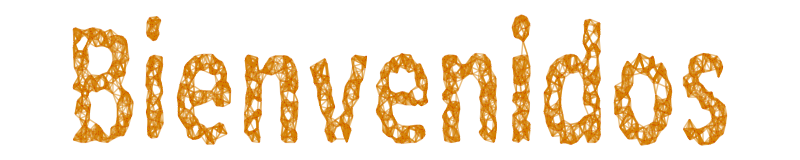

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
f = Sum[-13 i^3-14^(-7i)+7^(10i),{i, 2, n-1}];
g = {7^(10n),n*7^(10n),n^9,n^8,n^7,n^6,n^5,n^4,n^3,n^2,n,1};
Table[i->Limit[f/i,n->Infinity],{i,g}]
```

{7^(10 n)→1/282475248,7^(10 n) n→0,n^9→∞,n^8→∞,n^7→∞,n^6→∞,n^5→∞,n^4→∞,n^3→∞,n^2→∞,n→∞,1→∞}

```mathematica
Limit[f/7^(10n),n->Infinity]
```

1/282475248

```mathematica
Limit[1/7^(10 n)Sum[-13 i^3-14^(-7i)+7^(10i),{i, 2, n-1}], n->Infinity]
```

1/282475248

```mathematica
Table[i,{i,1,50,10}]
```

{1,11,21,31,41}

```mathematica
Clear[f,g]
```

```mathematica
f=Product[2^i/(16 i^2),{i,2, n-1}];

g=(2^(n^2))/(n!);
Limit[f/g, n->Infinity]
```

0

```mathematica
Limit[Sum[1,{i, 1,n^3+2}]/n^3,n->Infinity]
```

1

```mathematica
g={n^2,n^3,n^5,n^6,n^4};
Table[i->Limit[1/i Sum[Sum[1, {j,1,i+6}],{i, 1,n^3+2}],n->Infinity],{i,g}]
```

{n^2→∞,n^3→∞,n^5→∞,n^6→1/2,n^4→∞}

```mathematica
f=(15 n^4+17 n^3+20 n^2-4n+16)/(6 n^4+13 n^3+19 n^2+17+16);
g=(15 n^j+10 n^2+3n+19)/(8 n^4-14 n^3+19 n^2-9n+11);
```

```mathematica
?CompLimit
```

```mathematica
CompLimit[{f,g},jvalor->100]
```

```mathematica
Programa1[n_,valor_:60/5846006549323611671624303190352640062064535163787]:=If[n==6,valor,Programa1[n-1,valor*((-(3+19 (-3+n)))/(-8^(18 (-3+n))+13^(9 (-3+n))-20^(7 (-3+n))))]]

Programa2[n_]:=If[n==6,60/5846006549323611671624303190352640062064535163787,Programa2[n-1]*((-(3+19 (-3+n)))/(-8^(18 (-3+n))+13^(9 (-3+n))-20^(7 (-3+n))))]

Programa3[n_]:=Module[{i,valor=1},For[i=3,i<=n-3,valor=valor*(3+19 i)/(8^(18 i)-13^(9 i)+20^(7 i));i++];
valor]

Programa4[n_]:=Product[(3+19 i)/(8^(18 i)-13^(9 i)+20^(7 i)),{i,3,n-3}]

PruebaADAGrafica[{Programa1,Programa2,Programa3,Programa4},25,6]
```

-Graphics-

```mathematica
PruebaADAGrafica[{Programa1,Programa2,Programa3,Programa4},30,6]
```

-Graphics-

```mathematica
{Programa1[6], Programa2[6]}
```

{60/5846006549323611671624303190352640062064535163787,60/5846006549323611671624303190352640062064535163787}